# Homework 3

Long Wang     1101110160      Work in Mathematica 8.0

## Question 2

### Code

```mathematica
q2data=Import["/Users/wanglong/Documents/lessons/Astronomy/distances/HW3/VCUslice.dat","Data"][[2;;]];
q2label=Import["/Users/wanglong/Documents/lessons/Astronomy/distances/HW3/VCUslice.dat","Data"][[1]];
```

```mathematica
q2datalist[1]=Sort[Cases[q2data,{x_,y_,z_,v_,sfr_}->{x,y,z,Sqrt[(x-50)^2+y^2+z^2],v,sfr}],#1[[4]]<#2[[4]]&];
q2datalist[2]=Select[q2datalist[1],#[[6]]==0&];
q2range={{0,20},{25,75},{100,200}};
q2style={"(All)","(Elliptical)"};
q2datafitlist=Table[LinearModelFit[Select[q2datalist[j],q2range[[i,1]]<#[[4]]<q2range[[i,2]]&][[All,{4,5}]],d,d],{j,2},{i,3}];
```

```mathematica
Needs["PlotLegends`"]
q2Plotyz[s_]:=ListPlot[Table[q2datalist[i][[All,{3,2}]],{i,2}],AxesLabel->{"z(Mpc)","y(Mpc)"},PlotLabel->"Large scale structure",ImageSize->s]
q2Plotxyz[s_]:=ListPointPlot3D[q2datalist[1][[All,1;;3]],AxesLabel->{"x","y","z"},ImageSize->s]
q2Plotfit[s_]:=Grid@Table[Plot[q2datafitlist[[j,i]][d],{d,q2range[[i,1]],q2range[[i,2]]},Epilog->First@ListPlot[q2datalist[j][[All,{4,5}]],PlotStyle->Red],PlotStyle->Automatic,PlotLabel->"v_r vs. d_sun "<>q2style[[j]]<>" ("<>ToString[q2range[[i,1]]]<>"-"<>ToString[q2range[[i,2]]]<>")(Mpc)",AxesLabel->{"d(Mpc)","v_r(km/s)"},ImageSize->s/2],{i,3},{j,2}]
q2Tablefit:=Grid[{{"","All","","Elliptical"},{"distance(Mpc)","H0(km·s^-1Mpc^-1)","H0_Err(km·s^-1Mpc^-1)","H0(km·s^-1Mpc^-1)","H0_Err(km·s^-1Mpc^-1)"}}~Join~Table[{ToString@q2range[[i,1]]<>"-"<>ToString@q2range[[i,2]]}~Join~q2datafitlist[[1,i]]["ParameterTableEntries"][[2,{1,2}]]~Join~q2datafitlist[[2,i]]["ParameterTableEntries"][[2,{1,2}]],{i,3}],Frame->All]
```

### Discussion

#### Large scale structure

The plots of y to z coordinates and 3-dimension are shown in Figure 2.1. We can see a lot of voids and maybe also filament and core struction. The red points are elliptical galaxies.

#### Hubble constant

Hubble constant can be calculated by linear fitting the light-of-sight velocity v_r vs. the distance of galaxies to the Sun d_sun. The coefficient of d_sunis the Hubble constant. The fitting result is listed in Table 2.1 and all fitting curves and data for different distance ranges and galaxy classes (All and elliptical galaxies) are shown in Figure 2.2.

The peculiar velocities’ influences are obvious for the sample of galaxies close to the sun. Some galaxies even have velocity towards the sun. The fitting result of Hubble constant of this sample (all galaxy types) is much larger than the other two samples. Since the closer galaxies will feel larger gravity from local group, which means that their light-of-sight velocity will be influenced more by gravity, the slope of fitting line should be larger than the other two samples’ and thus leads to larger Hubble constant.

If I only analyze the ellipital galaxies, I find the results of samples with large distance to the Sun are similar to the samples of same distance range and all types of galaxies. But the error bars are larger. The sample of close galaxies contain two small number of galaxies so that it cannot used to calculate the Hubble constant.

Besides, from the Figure 2.2, we can see that the elliptical galaxies number density respect to the distance to the Sun shows several peaks.

### Figures & Tables

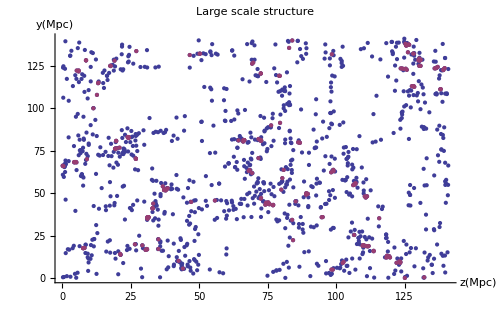

-Graphics3D-

Figure 2.1: Galaxies distribution. up) projected on y-z plane; bottom) 3-dimension

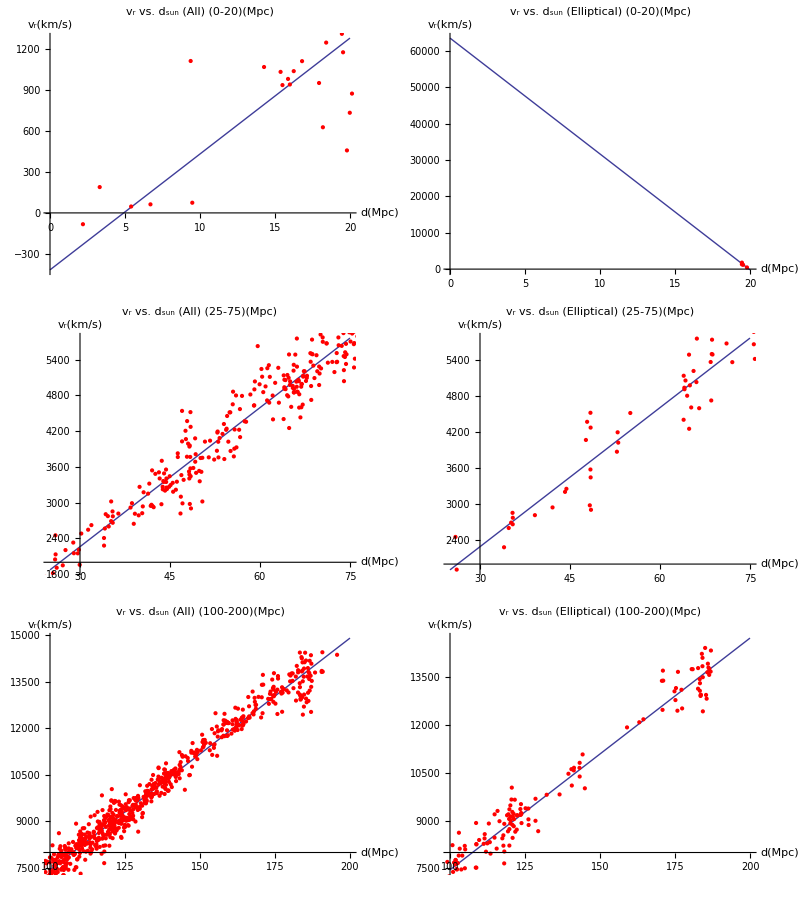

Figure 2.2: Linear fitting result of light-to-sight velocity vs. distance to the Sun

Table 2.1: Fitting parameters

| All |  | Elliptical | 
distance(Mpc) | H0(km·s^-1Mpc^-1) | H0_Err(km·s^-1Mpc^-1) | H0(km·s^-1Mpc^-1) | H0_Err(km·s^-1Mpc^-1)
0-20 | 85.0333 | 14.9636 | -3184.65 | 892.21
25-75 | 77.7839 | 1.50428 | 77.1887 | 4.30767
100-200 | 74.5738 | 0.528311 | 72.8352 | 1.36311

```mathematica
(************Code part, don't pay attention here************)
q2Plotyz[500]
q2Plotxyz[500]
"Figure 2.1: Galaxies distribution. up) projected on y-z plane; bottom) 3-dimension"
q2Plotfit[500]
"Figure 2.2: Linear fitting result of light-to-sight velocity vs. distance to the Sun"
"Table 2.1: Fitting parameters"
q2Tablefit
(************End of code part*************)
```

## Question 3

### Code

```mathematica
q3data=Import["/Users/wanglong/Dropbox/Datas/distances/hw3/fgc_s.dat","Data"];
q3label={"TYPE","log(σ)","log(r_e)",",⟨μ⟩_e","log(r_n)","log(r_e)",",⟨μ⟩_e","log(r_n)","c_4","ϵ"};
q3data2=Import["/Users/wanglong/Dropbox/Datas/distances/hw3/fgs.dat","Data"];
q3label2={"Name","log(r_e)","⟨μ⟩_e","(B-r)","log(σ)"};
```

```mathematica
q3datalist1=Cases[q3data,{t_,s_,r_,m_,x___}->{s,-0.4(m-26.4),r}];
q3datalist2=Cases[q3data2,{n_,r_,m_,br_,s_}->{s,-0.4(m+br-26.4),r}];
q3datafit1=LinearModelFit[q3datalist1,{s,i},{s,i}];
(*q3datafit2=NonlinearModelFit[q3datalist2,{A*s+B*i+c,Abs[A-1.232160233548455]<0.10747173055976973,Abs[B+0.8566307927631042]<0.03582649048127458},{{A,1.232160233548455},{B,0.8566307927631042},c},{s,i}];*)
q3fp[size_]:=Show[{ListPlot3D[q3datalist1,PlotStyle->{Opacity[0.5],Pink}],ListPointPlot3D[q3datalist1,Filling->Bottom,PlotStyle->PointSize[Large]],Plot3D[q3datafit1[s,i],{s,2,2.6},{i,1.3,2.7},PlotStyle->{Opacity[0.3],Green},Mesh->None]},PlotLabel->"Fundamental Plane of Coma data with Linear Fit",AxesLabel->{"Log[σ]","Log,⟨I⟩","Log[r_e]"},ImageSize->size,ViewPoint->{-2,0,1}]
```

```mathematica
q3datalist2c={#1,#2,#3-q3datafit1[#1,#2]}&@@@q3datalist2;
q3fps[size_]:=Show[{ListPlot3D[q3datalist2,PlotStyle->{Opacity[0.5],Pink}],ListPointPlot3D[q3datalist2,Filling->Bottom,PlotStyle->PointSize[Large]],Plot3D[q3datafit1[s,i],{s,1.6,2.5},{i,1.5,2.8},PlotStyle->{Opacity[0.3],Green},Mesh->None]},PlotLabel->"Fundamental Plane of S639 data",AxesLabel->{"Log[σ]","Log,⟨I⟩","Log[r_e]"},ImageSize->size,ViewPoint->{-1,-1,0}]
q3fpsr[size_]:=ListPointPlot3D[q3datalist2c,Filling->Bottom,AxesLabel->{"Log[σ]","Log,⟨I⟩","ΔLog[r_e]"},PlotLabel->"Residual of S639 data minus FP estimation",ViewPoint->Front]
q3fpd=Mean@q3datalist2c[[All,3]];
q3fpvar=StandardDeviation@q3datalist2c[[All,3]];
```

### Discussion

#### Derive Fundamental Plane

To derive the Johnson-B band Fundamental Plane (FP), I use 21 galaxies from Table 1 of [1]. My dataset excludes S0, E/S0 galaxies and also No. 107. Then I use linear fitting to fit Log[R_e](log[σ], log⟨I⟩). The result is:
	Log[R_e] =1.23log[σ]-0.86log⟨I⟩-0.13     (3.1)
The coefficients are slight different from the equation given in the question paper but they are consistent with each other considering the standard error.

#### Calculate FP distance and peculiar velocity for S639

Then I inputs S639 data [2] to FP fitting function Eq. 3.1 and obtain the predicted (Log[R_e])_p. The mean of  residual of the predicted one and observed one is:
	ΔLog[R_e]= ∑[(Log[R_e])_p-Log[R_e]] = 0.17 ±0.12
If assume Coma cluster is not affected by peculiar motion, From its velocity of recession v_c=cz_e=7008 km s^-1 and Hubble’s law v=H_0d. We can get its distance d_c=v_c/H_0=7008/72 Mpc=97.33Mpc. Since the surface brightness and velocity dispersion is independent of distance, only angular effect radius of galaxy R_e(arcsec) will vary with distance varying. Then we can get R_e(arcsec)d=R_e(pc) is constant for the same size galaxy at different distance. Thus the S639 FP distance can be estimated as:
	d_s/d_c=((R_e)_p)/R_e=10^(0.17±0.12)
	d_s=10^(0.17±0.12)×97.33Mpc=143.96±39.78Mpc
If we assume S639 is not affected by peculiar motion, from Hubble’s law, we can get its velocity of recession 
	(v_s)_rec=H_0 d_s=(143.96±39.78)×72 km s^-1=10364±2864km s^-1
The observed light-of-sight velocity of S639 (v_s)_o=cz_s=6545km s^-1, so its peculiar velocity can be estimated as:
	(v_s)_p=(v_s)_o-(v_s)_rec=-3819±2864 km s^-1
It means that S639’s peculiar velocity is towards us. There is some massive sources near us attract S639 with gravity. 
The error here is very large, which may be caused by the color correction for B-band since we assume a constant (B-V) for some data.

### Figures & Tables

```mathematica
(************Code part, don't pay attention here************)
"Table 3.1: 21 galaxies of Coma"
Grid[Prepend[q3data,q3label],Frame->All]
q3fp[500]
"Figure 3.1: Fundamental Plane of Coma. Blue dots are 21 galaxies data points from Table 1 of Jorgensen et al., 1993. Pink surface is data surface. Green plane is the linear fitting plane."
"Table 3.2: Linear Fitting parameters for 21 galaxies data. s is Log[σ], i is Log⟨I⟩, 1 is zero-point"
q3datafit1["ParameterTable"]
"Table 3.3: S639 galaixes data"
Grid[Prepend[q3data2,q3label2],Frame->All]
q3fps[500]
"Figure 3.2: Fundamental Plane of S639. Blue dots are data points from Jorgensen et al., 1998. Pink surface is data surface. Green plane is the fitting function plane from Coma data."
q3fpsr[500]
"Figure 3.3: Residual of S639 minus fitting FP function plane from Coma data. The means value of this residual is "<>ToString@SetPrecision[q3fpd,2]<>" and its standard deviation is "<>ToString@SetPrecision[q3fpvar,2]<>"."
(************End of code part*************)
```

Table 3.1: 21 galaxies of Coma

TYPE | log(σ) | log(r_e) | ,⟨μ⟩_e | log(r_n) | log(r_e) | ,⟨μ⟩_e | log(r_n) | c_4 | ϵ
E | 2.431 | 1.1 | 21.24 | 0.95 | 1.06 | 19.89 | 0.97 | -0.009 | 0.132
E | 2.301 | 0.78 | 20.81 | 0.77 | 0.77 | 19.6 | 0.77 | 0.007 | 0.135
E | 2.176 | 0.71 | 20.98 | 0.64 | 0.65 | 19.61 | 0.64 | 0. | 0.073
E | 2.312 | 0.97 | 21.31 | 0.81 | 0.93 | 19.97 | 0.83 | -0.003 | 0.103
E | 2.225 | 0.96 | 21.6 | 0.71 | 0.93 | 20.33 | 0.72 | -0.006 | 0.127
E | 2.26 | 0.79 | 20.95 | 0.73 | 0.8 | 19.82 | 0.74 | 0.001 | 0.306
E | 2.223 | 0.28 | 19.63 | 0.57 | 0.27 | 18.47 | 0.57 | 0.007 | 0.057
D | 2.389 | 1.75 | 23.12 | 0.98 | 1.73 | 21.85 | 1. | 0.004 | 0.112
E | 2.346 | 0.58 | 20.01 | 0.77 | 0.54 | 18.78 | 0.76 | 0.003 | 0.283
E | 2.262 | 0.27 | 19.65 | 0.55 | 0.23 | 18.3 | 0.56 | 0.016 | 0.25
E | 2.348 | 1.36 | 22.58 | 0.78 | 1.3 | 21.18 | 0.81 | -0.006 | 0.269
D | 2.581 | 1.54 | 21.94 | 1.18 | 1.51 | 20.59 | 1.2 | -0.004 | 0.364
E | 2.025 | 0.85 | 21.68 | 0.56 | 0.78 | 20.34 | 0.55 | 0.006 | 0.088
E | 2.215 | 1.06 | 21.83 | 0.74 | 1.02 | 20.57 | 0.73 | 0.004 | 0.018
SBO | 2.205 | 1.06 | 22.3 | 0.59 | 1.05 | 21.09 | 0.59 | 0.034 | 0.334
E | 2.13 | 0.68 | 21.22 | 0.54 | 0.66 | 19.98 | 0.55 | 0.003 | 0.008
E | 2.297 | 0.95 | 21.18 | 0.82 | 0.93 | 19.95 | 0.83 | 0 | 0.158
E | 2.324 | 0.73 | 20.37 | 0.83 | 0.69 | 19.03 | 0.84 | 0.009 | 0.332
E | 2.34 | 1.07 | 21.54 | 0.84 | 1.07 | 20.38 | 0.84 | 0.002 | 0.048
E | 2.36 | 1.07 | 21.54 | 0.84 | 0.99 | 20.1 | 0.84 | 0.004 | 0.037
E | 2.422 | 1.3 | 21.73 | 1.01 | 1.24 | 20.4 | 1.01 | -0.009 | 0.165

-Graphics3D-

Figure 3.1: Fundamental Plane of Coma. Blue dots are 21 galaxies data points from Table 1 of Jorgensen et al., 1993. Pink surface is data surface. Green plane is the linear fitting plane.

Table 3.2: Linear Fitting parameters for 21 galaxies data. s is Log[σ], i is Log⟨I⟩, 1 is zero-point

| Estimate | Standard Error | t-Statistic | P-Value
1 | -0.131749 | 0.26989 | -0.488157 | 0.631332
s | 1.23216 | 0.107472 | 11.465 | 1.0479×10^-9
i | -0.856631 | 0.0358265 | -23.9105 | 4.32518×10^-15

Table 3.3: S639 galaixes data

Name | log(r_e) | ⟨μ⟩_e | (B-r) | log(σ)
E264G23 | 1.24 | 20.63 | 1.14 | 2.342
E264G24 | 0.97 | 18.92 | 1.06 | 2.349
E261G26 | 1.18 | 20.74 | 1.1 | 2.115
E264G28 | 1.46 | 21.44 | 1.1 | 2.191
E264G300 | 1.18 | 20.01 | 1.15 | 2.449
E264G301 | 0.66 | 18.91 | 1.11 | 2.265
E264G302 | 0.6 | 18.83 | 1.17 | 2.276
E264G31 | 1.28 | 20.35 | 1.11 | 2.392
J06 | 0.99 | 20.41 | 1.1 | 2.041
J09 | 0.59 | 20.43 | 1.1 | 1.852
J1O | 0.85 | 21.5 | 1.1 | 1.856
J13 | 0.84 | 19.08 | 1.13 | 2.298
J14 | 0.89 | 19.76 | 1.09 | 2.135
J15 | 0.49 | 18.73 | 1.09 | 2.105
J16 | 0.61 | 19.6 | 1.11 | 2.094
J18 | 0.39 | 19.91 | 1.1 | 1.935
J20 | 0.52 | 20.38 | 1.1 | 1.633
J23 | 0.38 | 18.64 | 1.13 | 2.14
J26 | 0.49 | 18.31 | 1.1 | 2.496
J31 | 0.81 | 20.98 | 1.1 | 1.715
J32 | 0.72 | 19.25 | 1.1 | 2.187
J101 | 0.73 | 20.76 | 1.1 | 1.96
J104 | 1.26 | 21.49 | 1.1 | 2.018
J109 | 1.15 | 21. | 1.1 | 2.154

-Graphics3D-

Figure 3.2: Fundamental Plane of S639. Blue dots are data points from Jorgensen et al., 1998. Pink surface is data surface. Green plane is the fitting function plane from Coma data.

-Graphics3D-

Figure 3.3: Residual of S639 minus fitting FP function plane from Coma data. The means value of this residual is 0.17 and its standard deviation is 0.12.

## Question 4

### Code

```mathematica
q4data1=Transpose@Import["/Users/wanglong/Dropbox/Datas/distances/hw3/dv.dat","Data"];
q4data3={{"SMC",0+52/60.0+ 44.8/3600.0,-72- 49/60.+43/3600.},{"LMC",05+23/60.+34.5/3600.,-69-45/60.-22/3600.},{"6822",19+44.9/60.0,-14-48/60.0},{"598",1+33.9/60.0,30+39/60.0},{"221",0+42.7/60.0,40+52/60.0},{"224",0+42.7/60.0,41+16/60.},{"5457",14+3.2/60.,54+21/60.},{"4736",12+50.9/60.,41+7/60.},{"5194",13+29.9/60.,47+12/60.},{"4449",12+28.2/60.,44+6/60.},{"4214",12+15.6/60.,36+20/60.},{"3031",9+55.6/60.,69+4/60.},{"3627",11+20.2/60.,12+59/60.},{"4826",12+56.7/60.,21+41/60.},{"5236",13+37.0/60.,-29-52/60.},{"1068",2+42.7/60.,-0-1/60.},{"5055",13+15.8/60.,42+2/60.},{"7331",22+37.1/60.,34+25/60.},{"4258",12+19.0/60.,47+18/60.},{"4151",12+10.5/60.,39+24/60.},{"4382",12+25.4/60.,18+11/60.},{"4472",12+29.8/60.,8.},{"4486",12+30.8/60.,12+24/60.},{"4649",12+43.7/60.,11+33/60.}};
q4data4=Table[q4data3[[i]]~Join~q4data1[[i]],{i,Length@q4data3}];
q4data5=Cases[q4data4,{n_,ra_,dec_,r_,v_}->{n,ra*15π/180,dec*π/180,r,v}];
q4data6=Cases[q4data5,{n_,ra_,dec_,r_,v_}->{n,r*Cos[dec]*Cos[ra],r*Cos[dec]*Sin[ra],r*Sin[dec],ra,dec,r,v,v+65*Cos[dec]Cos[ra]-226*Sin[ra]Cos[dec]+195*Sin[dec]}];
q4data2=Transpose@Import["/Users/wanglong/Dropbox/Datas/distances/hw3/dv2.dat","Data"];
q4data7=FindClusters[Sort[q4data6[[All,2;;4]],Larger],9];
```

```mathematica
q4data7={{{0.00921069336183226,0.0021580874063811674,-0.030569687380487195},{0.0018619300101737264,0.011616303327453456,-0.03189976040100941}},{{0.09142864483806615,-0.18560306516565198,-0.05466539219825918}},{{0.7584187635372686,0.6517675156822815,-0.00029088820456342463}},{{0.20753174138257607,0.09012971688649382,0.13407539092867132},{0.20436532840143576,0.03852288242749498,0.17993276543434417},{0.20312593010968466,0.03828925574019223,0.18138023434745495}},{{-0.22528331245343913,-0.13429580720635478,0.36566660402175055},{-0.36743410342527716,-0.08297333373651516,0.32879721034204595},{-0.3139176529811809,-0.12986850515400022,0.3668649322514382},{-0.44899901445823615,-0.055527922296689965,0.4384250618531581},{-0.6429745754301459,-0.04383360905444457,0.47398555892314465},{-0.27533550103588283,0.16609299301935926,0.840597097032336},{-0.8638010030151592,0.15153429678143016,0.2022008508611242},{-0.8108521716809218,-0.20480072948241204,0.33252882113255217}},{{-0.7116010526386891,-0.32055290074552645,-0.44818498380371724}},{{-0.7727497805151823,-0.26532501047542667,0.7365191209533888},{-0.9461627450461059,-0.07862006133638008,1.0288804332099437},{-1.3122686405818775,-0.060163547586978706,1.0790418724438549}},{{0.8487230660518362,-0.3211289937457942,0.6217276948370439}},{{-1.8884681102790926,-0.21015706729024503,0.6241171392670425},{-1.9638172227023303,-0.256798184756716,0.2783462019201309},{-1.9357316389127457,-0.2617211859555751,0.4294706543341264},{-1.9239869267065177,-0.37137218596158333,0.4004460080416894}}};
q4data8=Table[Table[Flatten@Select[q4data6,#[[2;;4]]==q4data7[[i,j]]&],{j,Length@q4data7[[i]]}],{i,9}];
q4data9=Table[Mean@q4data8[[i,All,2;;9]],{i,9}];
q4data10=Cases[q4data9,{x_,y_,z_,ra_,dec_,r_,v_,vc_}->{x,y,z,ra,dec,Sqrt[x^2+y^2+z^2],v,vc,v-3.*Cos[dec]Cos[ra]-230.*Sin[ra]Cos[dec]+133.*Sin[dec]}];
q4fitvr=LinearModelFit[q4data10[[All,{6,9}]],{1,k},k];
q4table:=Column[Grid[#,Frame->All,ItemSize->{{2.4,3.8,3.8,3.8,3,4,4,5,5}}]&/@Prepend[SetPrecision[q4data8,2],{{"Name","x","y","z","RA","Dec","r","v","v_c"}}],Frame->All]
q4vr[s_]:=Show[{ListPlot[q4data8[[All,All,{7,9}]],PlotStyle-> Transpose@{Table[PointSize[Medium],{i,9}],RGBColor@@@(Tuples[{0,1},3][[1;;7]]~Join~{{0.5,0,1},{0,0.5,1}})}],ListPlot[q4data10[[All,{6,9}]],PlotMarkers->-Graphics-],Plot[q4fitvr[x],{x,0,2}]},AxesLabel->{"r(Mpc)","v(km/s)"},ImageSize->s]
q4position[size_]:=ListPointPlot3D[q4data7,AxesLabel->{"x","y","z"},AxesOrigin->{0,0,0},Filling->Axis,PlotStyle->Transpose@{Table[PointSize[i/1000+0.02],{i,9}],RGBColor@@@(Tuples[{0,1},3][[1;;7]]~Join~{{0.5,0,1},{0,0.5,1}})},PlotRange->Table[{-#,#}&@(Max@q4data5[[All,4]]),{i,3}],BoxRatios->{1,1,1},ImageSize->size]
q4fittable:=Column[{q4fitvr["ParameterTable"],Grid[Transpose[{#,q4fitvr[#]}&[{"AdjustedRSquared","RSquared"}]],Alignment->Left,Dividers->{2->True,1->True}]}]
```

```mathematica
c=3*^5;
q4sdata1=Import["/Users/wanglong/Dropbox/Datas/distances/hw3/sdata.dat","Data"];
q4slabel={"SN","z","μ","μ_err"};
q4sfit=NonlinearModelFit[q4sdata1[[All,2;;3]],25+5Log10[c*Zz/Subscript[H, 0]]+1.086(1-Subscript[q, 0])Zz,{Subscript[H, 0],Subscript[q, 0]},Zz];
q4sdata2=SplitBy[Sort[q4sdata1,#1[[2]]<#2[[2]]&],#[[2]]<0.7&];
q4sfit2=Table[NonlinearModelFit[q4sdata2[[i,All,2;;3]],25+5Log10[c*Zz/Subscript[H, 0]],Subscript[H, 0],Zz],{i,2}];
q4sfit3=Table[NonlinearModelFit[q4sdata2[[i,All,2;;3]],25+5Log10[c*Zz/Subscript[H, 0]]+1.086(1-Subscript[q, 0])Zz,{Subscript[H, 0],Subscript[q, 0]},Zz],{i,2}];
q4splot[s_]=Show[{ListPlot[q4sdata1[[All,2;;3]]],Plot[q4sfit[x],{x,0,2},PlotStyle->Black]}~Join~Table[Plot[q4sfit3[[i]][x],{x,0.7(i-1),0.7+1.1(i-1)},PlotStyle->{RGBColor[{i-1,2-i,0}],Dashed}],{i,2}],AxesLabel->q4slabel[[2;;3]],ImageSize->s];
q4stable:=TableForm[#["ParameterTable"]&/@({q4sfit}~Join~q4sfit3),TableHeadings->{{"z∈All","z<0.7","z≥0.7"}}]
```

### Discussion

#### Hubble data fitting

I redraw the radial velocity vs. distance figure from the Table 1 data of Hubble [3]. In his paper, He did not use the Table 1 data directly. Instead he corrected the solar motion so the corrected volecity: 
	v_c=v-X cos α cos δ + Y sin α cos δ + Z sin δ
α and δ here are RA and Dec, X, Y and Z can be found in [3]. The same correction is also used for groups of data. 

When I try a lot to get the same 9 groups as Hubble’s based on the directions and distances of these 24 nebulae data, I find it’s quite difficult for me to succeed since it seems there is no obvious criterion to split the data into 9 groups. So finally I have to split the data to 9 different groups. My method is using “Findclusters” function in Mathematica 8. This function finds clustering by local optimization. Since it depend on the orders of input data, I modify the result a little. The result is shown in Table 4.1 and Figure 4.1, 4.2. 

I then use linear fitting to get K. The fitting paremters are listed in Table 4.2. My fitting K = 538 ± 89 km/s/Mpc is consistent with Hubble’s K_H=513±60km/s/Mpc.

To calculate the age of universe, we should firstly know the geometry and matter distribution of universe. But at Hubble’s era, they did not know the acceleration rate of expanding of universe so that cannot constrain any Ω. If assuming universe is flat, we can only estimate the age of universe as 1/H_0≃1/(513km/s/Mpc)=1.91Gyr

#### Supernove data

Using function
	μ=25+5log((c z)/H_0)+1.086(1-q_0)z
I can fit the SNe μ vs. z well. The fitting result is listed in Table 4.3. I find that q_0 is only 0.2, which means that we cannot ignore it if we want to fit the data well. 

If I split the samples of SNe to two subsets by criterion whether z is less than 0.7 and then fit the subsets with same functions, I find Hubble constant is 46 +± 4 km/s/Mpc at high-redshift and 65 +± 1 km/s/Mpc at low-redshift and deceleration paramter q_0 is negative at low-redshift and positive at high-redshift. q_0is defined as:
	q_0=-1/(H_0^2 a(t_0)) (ⅆ^2 a(t))/(ⅆ t^2)|_(t=t_0)
Whether the universe is accelerating and decelerating is not determined by H_0but by q. But q_0only show the decelaration today. So the inconsistent data fitting of low-redshift and high-redshift cannot conclude whether the universe is accelerating or deceleration. But from all region fitting we see that the universe may be decelerating now since q_0is larger than 0. However, the series expansion fitting is dangerous to determine the high order coefficients like q_0 since series may not converge well at high orders. So we still cannot conclude whether the universe is constant, accelerating or decelerating.

### Figures & Tables

Table 4.1: Data used here. x, y, z are rectangular cooridates of sources. v_c is velocitie corrected for solar motion

Name | x | y | z | RA | Dec | r | v | v_c
SMC | 0.0092 | 0.0022 | -0.031 | 0.23 | -1.3 | 0.032 | 170. | -13.
LMC | 0.0019 | 0.012 | -0.032 | 1.4 | -1.2 | 0.034 | 290. | 33.
6822 | 0.091 | -0.19 | -0.055 | 5.2 | -0.26 | 0.21 | -130. | 44.
1068 | 0.76 | 0.65 | -0.00029 | 0.71 | -0.00029 | 1. | 920. | 820.
598 | 0.21 | 0.09 | 0.13 | 0.41 | 0.53 | 0.26 | -70. | 3.3
221 | 0.2 | 0.039 | 0.18 | 0.19 | 0.71 | 0.28 | -190. | -41.
224 | 0.2 | 0.038 | 0.18 | 0.19 | 0.72 | 0.28 | -220. | -75.
5457 | -0.23 | -0.13 | 0.37 | 3.7 | 0.95 | 0.45 | 200. | 390.
4736 | -0.37 | -0.083 | 0.33 | 3.4 | 0.72 | 0.5 | 290. | 410.
5194 | -0.31 | -0.13 | 0.37 | 3.5 | 0.82 | 0.5 | 270. | 430.
4449 | -0.45 | -0.056 | 0.44 | 3.3 | 0.77 | 0.63 | 200. | 310.
4214 | -0.64 | -0.044 | 0.47 | 3.2 | 0.63 | 0.8 | 300. | 380.
3031 | -0.28 | 0.17 | 0.84 | 2.6 | 1.2 | 0.9 | -30. | 91.
3627 | -0.86 | 0.15 | 0.2 | 3. | 0.23 | 0.9 | 650. | 590.
4826 | -0.81 | -0.2 | 0.33 | 3.4 | 0.38 | 0.9 | 150. | 210.
5236 | -0.71 | -0.32 | -0.45 | 3.6 | -0.52 | 0.9 | 500. | 430.
5055 | -0.77 | -0.27 | 0.74 | 3.5 | 0.73 | 1.1 | 450. | 590.
4258 | -0.95 | -0.079 | 1. | 3.2 | 0.83 | 1.4 | 500. | 610.
4151 | -1.3 | -0.06 | 1.1 | 3.2 | 0.69 | 1.7 | 960. | 1000.
7331 | 0.85 | -0.32 | 0.62 | 5.9 | 0.6 | 1.1 | 500. | 730.
4382 | -1.9 | -0.21 | 0.62 | 3.3 | 0.32 | 2. | 500. | 520.
4472 | -2. | -0.26 | 0.28 | 3.3 | 0.14 | 2. | 850. | 840.
4486 | -1.9 | -0.26 | 0.43 | 3.3 | 0.22 | 2. | 800. | 810.
4649 | -1.9 | -0.37 | 0.4 | 3.3 | 0.2 | 2. | 1100. | 1100.

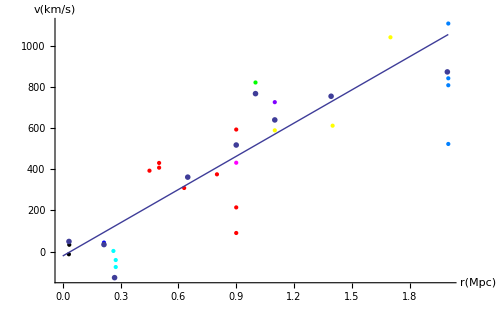

Figure 4.1: Velocity-Distance relation. Color points are 24 nebulae data. 9 open circles are groups data. Blue line is fitting line.

Table 4.2: Fitting parameters of 9 groups data of v_c vs. r, 1 is constant parameter and k is first order coefficient.

| Estimate | Standard Error | t-Statistic | P-Value
1 | -21.2395 | 91.1674 | -0.232973 | 0.822448
k | 538.264 | 88.8375 | 6.05897 | 0.000511393
AdjustedRSquared | 0.81698
RSquared | 0.839858

-Graphics3D-

Figure 4.2: Positions of all nebulae. 9 different colors represent different groups

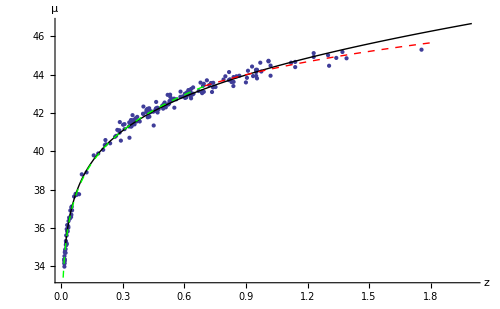

Figure 4.3: μ vs. z for SNe data and fitting curve. Blue points are SNe data. Black solid curve fits all redshift region. Green dashed curves fit z<0.7 and red dashed curves fit z>0.7.

Table 4.3: Fitting parameters for μ vs. z of SNe data for three redshift region

z∈All |  | Estimate | Standard Error | t-Statistic | P-Value
H_0 | 61.6582 | 0.854288 | 72.175 | 4.78381×10^-140
q_0 | 0.201234 | 0.0463958 | 4.33732 | 0.0000233865
z<0.7 |  | Estimate | Standard Error | t-Statistic | P-Value
H_0 | 64.6366 | 0.948019 | 68.1807 | 4.7667×10^-112
q_0 | -0.117845 | 0.0734388 | -1.60467 | 0.110743
z≥0.7 |  | Estimate | Standard Error | t-Statistic | P-Value
H_0 | 46.1079 | 3.60378 | 12.7943 | 2.95679×10^-16
q_0 | 0.83278 | 0.156255 | 5.32963 | 3.41718×10^-6

```mathematica
(************Code part, don't pay attention here************)
"Table 4.1: Data used here. x, y, z are rectangular cooridates of sources. v_c is velocitie corrected for solar motion"
q4table
q4vr[500]
"Figure 4.1: Velocity-Distance relation. Color points are 24 nebulae data. 9 open circles are groups data. Blue line is fitting line."
"Table 4.2: Fitting parameters of 9 groups data of v_c vs. r, 1 is constant parameter and k is first order coefficient."
q4fittable
q4position[500]
"Figure 4.2: Positions of all nebulae. 9 different colors represent different groups"
q4splot[500]
"Figure 4.3: μ vs. z for SNe data and fitting curve. Blue points are SNe data. Black solid curve fits all redshift region. Green dashed curves fit z<0.7 and red dashed curves fit z>0.7."
"Table 4.3: Fitting parameters for μ vs. z of SNe data for three redshift region"
q4stable
(************End of code part*************)
```

## Reference

1.	Jorgensen et al. (1993), ApJ, 411, 34

2.	Jorgensen & Jonch--Sorensen (1998), MNRAS, 297, 968

3.	E. Hubble (1929), Proc. Natl. Acad. Sci. USA 15, 168